# Lab 11

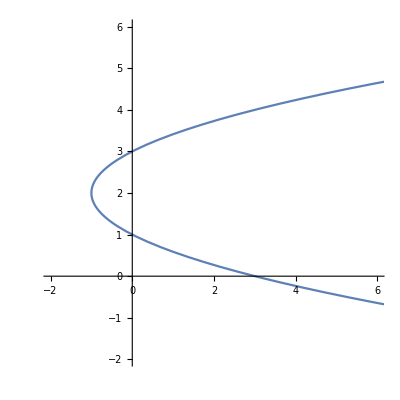

```mathematica
ParametricPlot[{t^2-2t,t+1},{t,-2,4},PlotRange->{-2,6}]
```

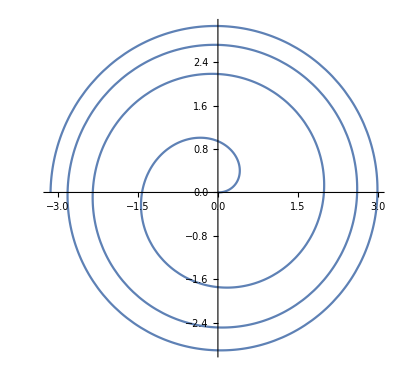

```mathematica
PolarPlot[Log[t+1],{t,0,7Pi}]
```

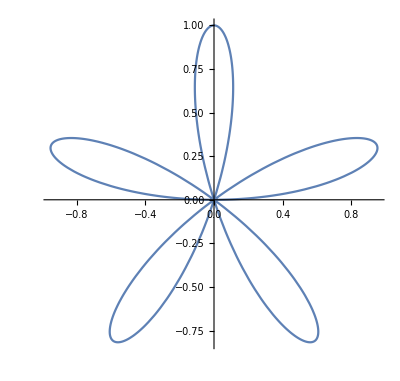

```mathematica
PolarPlot[Sin[5t],{t,0,Pi}]
```

## Question 1

```mathematica
x[t_]=4Cos[t]-Cos[16t]
```

4 Cos[t]-Cos[16 t]

```mathematica
y[t_]=4Sin[t]-Sin[16t]
```

4 Sin[t]-Sin[16 t]

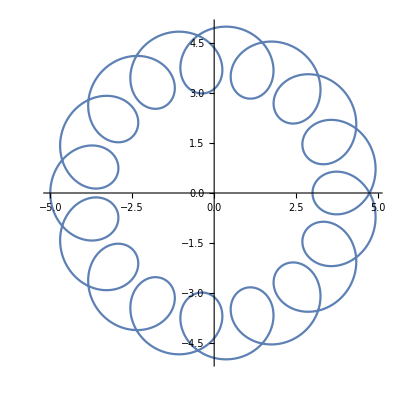

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,2Pi},PlotRange->Automatic]
```

## Question 2

```mathematica
x2[t_]=t-Sin[t]
```

t-Sin[t]

```mathematica
y2[t_]=1-Cos[t]
```

1-Cos[t]

```mathematica
x2'[t]
```

1-Cos[t]

```mathematica
y2'[t]
```

Sin[t]

```mathematica
y2'[Pi/4]/x2'[Pi/4]
```

1/(√2 (1-1/(√2)))

```mathematica
N[1/(√2 (1-1/(√2)))]
```

2.41421

## Question 3

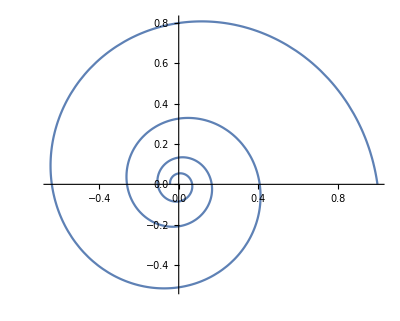

```mathematica
PolarPlot[Exp[-t/7],{t,0,7Pi}]
```

## Question 4

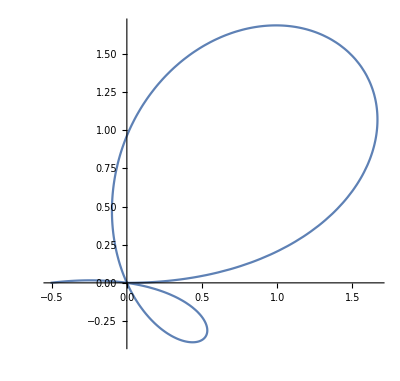

```mathematica
PolarPlot[t*(2-t)*(3-t),{t,0,Pi}]
```